```mathematica
alldata=Import[FileNameJoin[{NotebookDirectory[],"fixtures","output.csv"}]];
```

```mathematica
dataset=Import[FileNameJoin[{NotebookDirectory[],"fixtures","dataset.csv"}]];
```

```mathematica
holidays=DayRange[DateObject[{2014,1,1}],DateObject[{2015,12,31}],"Holiday",HolidayCalendar->{"UnitedStates", "Default"}]
```

{Wed 1 Jan 2014,Mon 20 Jan 2014,Mon 17 Feb 2014,Mon 26 May 2014,Fri 4 Jul 2014,Mon 1 Sep 2014,Mon 13 Oct 2014,Tue 11 Nov 2014,Thu 27 Nov 2014,Thu 25 Dec 2014,Thu 1 Jan 2015,Mon 19 Jan 2015,Mon 16 Feb 2015,Mon 25 May 2015,Fri 3 Jul 2015,Mon 7 Sep 2015,Mon 12 Oct 2015,Wed 11 Nov 2015,Thu 26 Nov 2015,Fri 25 Dec 2015}

```mathematica
extractDataByYear[l_List,y_Integer]:=Select[l,DateValue[First[#],"Year"]==DateValue[{y},"Year"]&]
```

```mathematica
extractDataByWeekday[l_List,w_Symbol]:=
Select[l,DayName[First[#]]==w&]
```

```mathematica
extractHourlyData[l_List]:=Map[Rest,l]
```

```mathematica
plotListWithModel[l_List,nlm_FittedModel]:=Show[Map[ListPlot,l],Plot[nlm[x],{x,0,24}],PlotRange->All,Ticks->{Range[24],Automatic}]
```

```mathematica
getSampleData[l_List,y_Integer,w_Symbol,n_Integer]:=extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,y],w]][[n]]
```

```mathematica
minMaxMeanPlot[l_List]:=Show[ListLinePlot[Map[Max,l],PlotStyle->Red],ListLinePlot[Map[Min,l],PlotStyle->Blue],ListLinePlot[Map[Mean,l],PlotStyle->Green],PlotRange->All]
```

```mathematica
nlm=NonlinearModelFit[getSampleData[dataset,2015,Monday,24],a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
```

FittedModel[1110.41-1073.15 x+255.375 x^2-16.7501 x^3+0.329474 x^4]

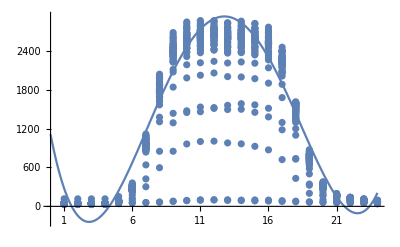

```mathematica
plotListWithModel[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2015],Monday]],nlm]
```

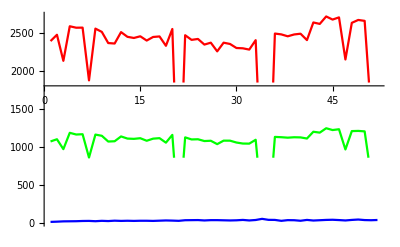

```mathematica
minMaxMeanPlot[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2014],Monday]]]
```

```mathematica
(*Extract all data in mondays which max numbers of parking cars is greater than 2000*)
```

```mathematica
selectedMondays=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[dataset,Monday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataBiased={DateValue[#1,"Hour"]}->#2&@@@Select[alldata,MemberQ[selectedMondays,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pBiased=Predict[trainingdataBiased]
```

PredictorFunction[…]

```mathematica
(*Extract all data in mondays*)
trainingdataUnbiased={DateValue[#1,"Hour"],MemberQ[holidays,DateObject[DateList[#1][[1;;3]]]]}->#2&@@@Select[alldata,(DateValue[First[#],"Year"]==DateValue[{2014},"Year"]|| DateValue[First[#],"Year"]==DateValue[{2015},"Year"])&&DayName[First[#]]==Monday&]
```

{{0,False}→22,{1,False}→17,{2,False}→16,{4,False}→39,{5,False}→186,{6,False}→749,{3,False}→15,{7,False}→1529,{8,False}→2160,{9,False}→2316,{10,False}→2363,{11,False}→2394,{12,False}→2363,{13,False}→2359,2468,{10,False}→1001,{11,False}→1007,{12,False}→979,{13,False}→965,{14,False}→927,{15,False}→872,{16,False}→722,{17,False}→432,{18,False}→201,{19,False}→103,{20,False}→68,{21,False}→59,{22,False}→48,{23,False}→40}
 |  |  |  |

```mathematica
pUnbiased=Predict[trainingdataUnbiased,Method->"RandomForest"]
```

PredictorFunction[…]

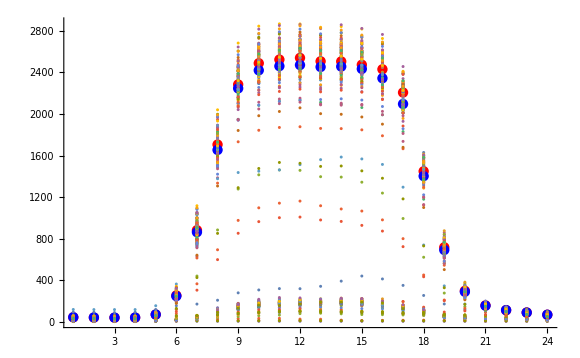

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[dataset,Monday]]],PlotRange->All]
```

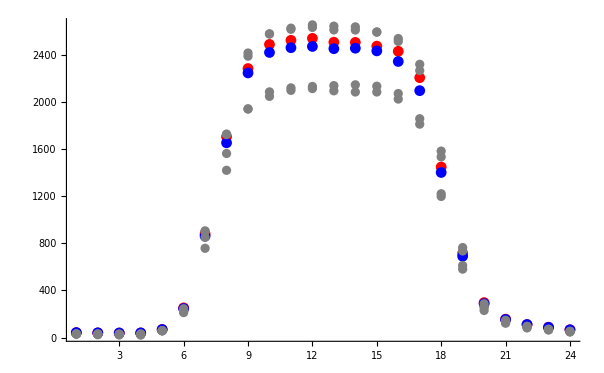

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Monday]],PlotStyle->Gray],PlotRange->All]
```